```mathematica
(* notebook to find energy density of stringbit *)
```

```mathematica
ClearAll[LoadEigenEnergies,LoadAndBucketEnergies,PlotEnergyBuckets];
DataFolder = NotebookDirectory[]<>"../data/";
Format[energy,StandardForm]="E";

Options[LoadEigenEnergies]={Folder->DataFolder,Bucketed->False, Single->False};
LoadEigenEnergies[s_,M_,opts:OptionsPattern[]]:=Module[{file,data},
file = "EEs="<> ToString[s] <> "M="<>ToString[M];
If[OptionValue[Bucketed], file = file <>"g"];
If[OptionValue[Single], file = file <>"s"];
data = Import[OptionValue[Folder]<> file <> ".txt", "Table"];
If[OptionValue[Bucketed]==False, data=Flatten[data]];
Return[data];
];

Options[LoadThermalData]={Folder->DataFolder};
LoadThermalData[s_,M_,opts:OptionsPattern[]]:=Module[{file,data},
file = "THs="<> ToString[s] <> "M="<>ToString[M];
data = Import[OptionValue[Folder]<> file <> ".txt", "Table"];
Return[data];
];

Options[LoadFluctuation]={Folder->DataFolder};
LoadFluctuation[s_,M_,opts:OptionsPattern[]]:=Module[{file,data},
file = "FLs="<> ToString[s] <> "M="<>ToString[M];
data = Import[OptionValue[Folder]<> file <> ".txt", "Table"];
Return[data];
];

PlotThermalData[s_,M_]:=Module[{data,Zdata,Edata,Sdata,ESdata,p1,p2,p3,p4},
data = LoadThermalData[s,M];
Zdata = Table[{data[[i, 1]],Log[data[[i,2]]]},{i,1,Length[data]}];
Edata = Table[{data[[i, 1]],data[[i,3]]},{i,1,Length[data]}];
Sdata = Table[{data[[i, 1]],data[[i,4]]},{i,1,Length[data]}];
ESdata = Table[{data[[i, 3]],data[[i,4]]},{i,1,Length[data]}];
p1=ListPlot[Zdata];
p2=ListPlot[Edata];
p3=ListPlot[Sdata];
p4=ListPlot[ESdata];
Return[{p1,p2,p3,p4}]
]

PlotFluctuation[s_,M_]:=Module[{data2,data,Z2},
data = LoadFluctuation[s,M];
Z2 = data[[1,2]]^2;
data2 = Table[{data[[i, 1]],(data[[i,2]]^2+data[[i,3]]^2)/Z2},{i,2,Length[data]}];
Return[ListPlot[data2]]
]


ClearAll[AverageEnergy];
Options[AverageEnergy]=Join[Options[LoadEigenEnergies],{}];
AverageEnergy[s_,M_, opts:OptionsPattern[]]:=Module[{data,data2,i,tot,count},
data = LoadEigenEnergies[s,M,FilterRules[{opts},Options[LoadEigenEnergies]]];
If[OptionValue[Bucketed]==False,
Return[Mean[data]],
tot=0;count=0;
For[i=1,i≤Length[data],i++,
tot += data[[i,1]] * data[[i,2]];
count += data[[i,2]]
];
Return[tot/count]
];
];

ClearAll[EnergyVariance];
Options[EnergyVariance]=Join[Options[LoadEigenEnergies],{}];
EnergyVariance[s_,M_, opts:OptionsPattern[]]:=Module[{data,data2},
data = LoadEigenEnergies[s,M,FilterRules[{opts},Options[LoadEigenEnergies]]];
data2=Table[data[[i]]^2,{i,1,Length[data]}];
Return[Mean[data2]-Mean[data]^2];
];

LoadAndBucketEnergies[s_,M_,n_]:=Module[{data,maxE,delta, buckets,i,pos},
data=LoadEigenEnergies[s,M];
maxE=N[4*s*Cot[Pi/(2M)]];
delta=2*maxE/n;
buckets=ConstantArray[0,n];
pos=Floor[(data+maxE)/delta] + 1;
For[i=1,i≤Length[pos],i++,
buckets[[pos[[i]]]]=buckets[[pos[[i]]]]+1;
];

Return[{Table[Chop[-maxE+delta*(i-0.5)],{i,1,n}],buckets}]
];

PlotEnergyBuckets[s_,M_,n_]:=Module[{data,i,list},
data=LoadAndBucketEnergies[s,M,n];
list=Table[{data[[1,i]],data[[2,i]]},{i,1,Length[data[[1]]]}];
(*Print[list];*)
ListPlot[list]
];

PlotEnergyBuckets[s_,M_]:=Module[{data,tot,ndata,fit,p1,p2,p3,delta,i},
data=LoadEigenEnergies[s,M,Bucketed->True];
tot=Sum[data[[i,2]],{i,1,Length[data]}];
delta=data[[2,1]]-data[[1,1]];
ndata=Table[{data[[i,1]],data[[i,2]]/(tot*delta)},{i,1,Length[data]}];
fit=FitEnergyData[ndata];
p1=ListPlot[ndata];
p2=Plot[fit[x],{x, -N[4*s*Cot[Pi/(2M)]],N[4*s*Cot[Pi/(2M)]]}];
Show[p1,p2]
];

FitEnergyData[ndata_]:=Module[{lmf},
lmf=NonlinearModelFit[ndata[[5;;Length[ndata]-5]], 
1/Sqrt[2*Pi*sigma^2]Exp[-(x-mu)^2/(2*sigma^2)],
{mu, sigma}, {x}];
Return[lmf]
];

FitEnergyData[s_, M_]:=Module[{data, lmf, tot,ndata,delta},
data=LoadEigenEnergies[s,M,Bucketed->True];
tot=Sum[data[[i,2]],{i,1,Length[data]}];
delta=data[[2,1]]-data[[1,1]];
ndata=Table[{data[[i,1]],data[[i,2]]/(tot*delta)},{i,1,Length[data]}];
lmf=FitEnergyData[ndata];
Return[{mu,sigma}/.lmf["BestFitParameters"]];
];
```

{{19,3.40773,13.5941},{20,3.42988,13.9151},{21,3.43427,14.1918},{22,3.43657,14.4681},{23,3.43993,14.7429},{24,3.44837,15.0185},{25,3.45235,15.2834},{26,3.45492,15.5443},{27,3.459,15.8029},{28,3.46212,16.0556},{29,3.46318,16.304},{30,3.46702,16.5498}}

{b→3.55811,c→2.6847}

{a→0.267142,b→8.57757}

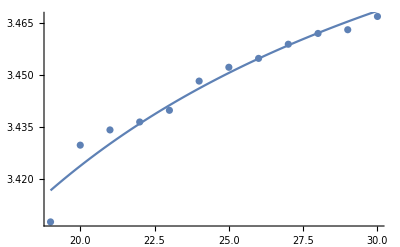

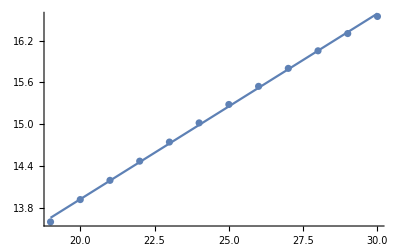

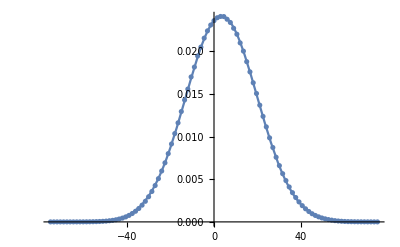

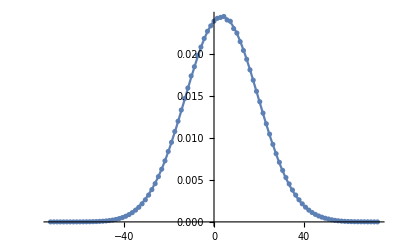

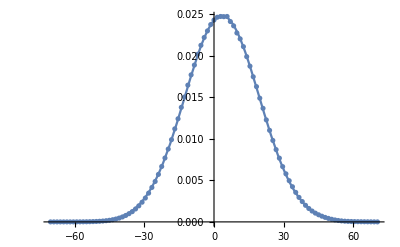

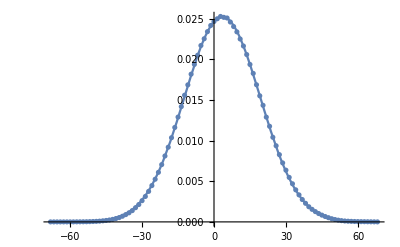

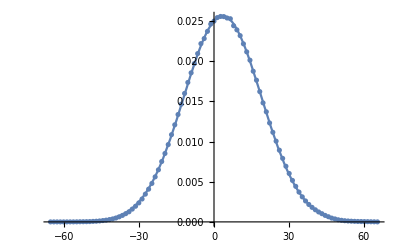

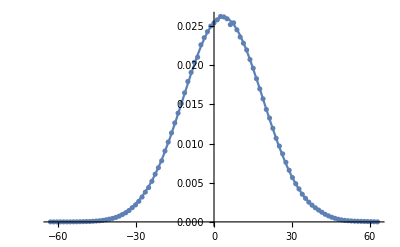

```mathematica
minM=19;
maxM = 30;
param=Table[Join[{m},FitEnergyData[1,m]],{m,minM,maxM}]
param1=param[[All,{1,2}]];
param2=param[[All,{1,3}]];
tfit1=NonlinearModelFit[param1, b-c/x,{ b,c}, {x}];
tfit2=NonlinearModelFit[param2, a*x+b,{a, b}, {x}];
tplot1=Plot[tfit1[x],{x,minM,maxM}];
tplot2=Plot[tfit2[x],{x,minM,maxM}];
tfit1["BestFitParameters"]
tfit2["BestFitParameters"]

Show[ListPlot[param[[All,{1,2}]]],tplot1]
Show[ListPlot[param[[All,{1,3}]]],tplot2]
PlotEnergyBuckets[1,30]
PlotEnergyBuckets[1,29]
PlotEnergyBuckets[1,28]
PlotEnergyBuckets[1,27]
PlotEnergyBuckets[1,26]
PlotEnergyBuckets[1,25]
PlotEnergyBuckets[1,24]
PlotEnergyBuckets[1,23]
PlotEnergyBuckets[1,22]
PlotEnergyBuckets[1,21]
PlotEnergyBuckets[1,20]
```

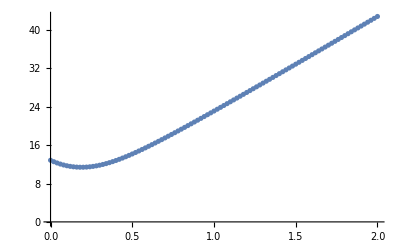

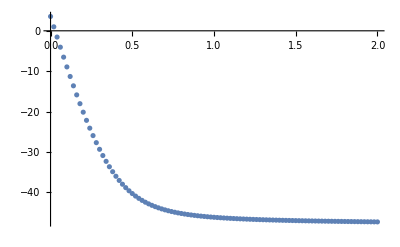

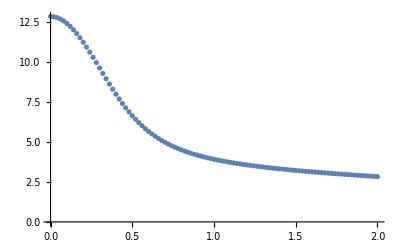

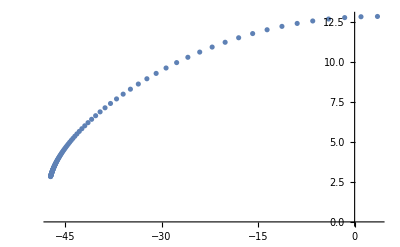

```mathematica
plots=PlotThermalData[1,19];
Show[plots[[1]]]
Show[plots[[2]]]
Show[plots[[3]]]
Show[plots[[4]]]
```

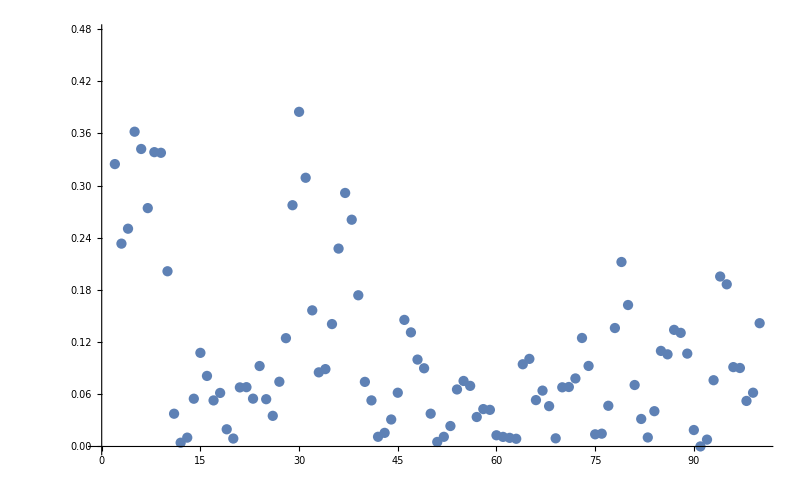

```mathematica
Show[PlotFluctuation[1,19]]
```